### Naloga 1

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

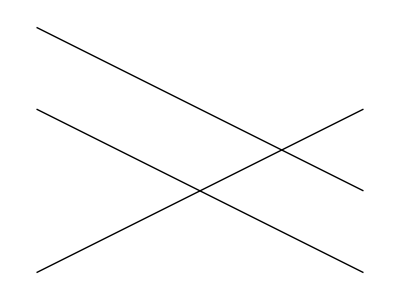

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

### Naloga 2

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

### Naloga 3

```mathematica
m1 = {{0,0},{1,1},{0,3},{-1,2}}
```

{{0,0},{1,1},{0,3},{-1,2}}

```mathematica
m2={{2,3},{1,9},{4,2},{7,0},{1,3}}
```

{{2,3},{1,9},{4,2},{7,0},{1,3}}

```mathematica
Slika[Mnogokotnika[t__]]:=Map[Line,List[t]]
```

```mathematica
Slika[Mnogokotnika[m1]]
```

{Line[{{0,0},{1,1},{0,3},{-1,2}}]}

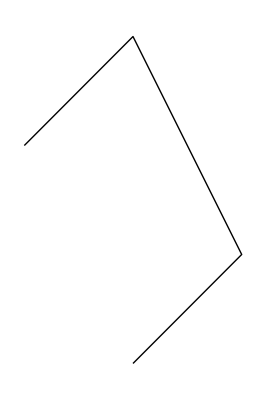

```mathematica
Graphics[Slika[Mnogokotnika[m1]]]
```

```mathematica
Narisi[m__Mnogokotnika]:=Graphics[Map[Slika,List[m]]]
```

```mathematica
Narisi[m1]
```

Narisi[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
NarobePravilniNKotnik[n_,r_]:=Module[{tocke, stej},
tocke =Table[{r Cos[(2 Pi + stej) /n], r Sin[(2 Pi + stej)/ n]},{stej,0,n - 1,1}];
Graphics[Slika[Mnogokotnika[tocke],Point[{0,0}]]]
]
```

```mathematica
Table[{5 Cos[(2 Pi + stej) /5], 5 Sin[(2 Pi + stej)/ 5]},{stej,0,4,1}] // N
```

{{1.54508,4.75528},{0.569557,4.96745},{-0.428677,4.98159},{-1.40982,4.79712},{-2.33476,4.42141}}

```mathematica
PravilniNKotnik[n_,r_]:= Graphics[{Line[Table[{r* Cos[(2Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]]},{Point[{0,0}]}]
```

```mathematica
PravilniNKotnik[5,2]
```

-Graphics-

### Naloga 4

### Naloga 5

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f, sez1,sez2],1]
```

```mathematica
VsiPari[f,{1,2,3},{a,b}]
```

{1/a,1/b,2/a,2/b,3/a,3/b}

```mathematica
?Outer
```

Outer[f,list_1,list_2,…] gives the generalized outer product of the list_i, forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to f. 
Outer[f,list_1,list_2,…,n] treats as separate elements only sublists at level n in the list_i. 
Outer[f,list_1,list_2,…,n_1,n_2,…] treats as separate elements only sublists at level n_i in the corresponding list_i.

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
f[x_,y_]:=x / y
```

```mathematica
VsiPari[f,{1,2,3},{-9,6,10,2}]
```

{-1/9,1/6,1/10,1/2,-2/9,1/3,1/5,1,-1/3,1/2,3/10,3/2}

```mathematica
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
```

```mathematica
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[f,m1,m2]
```